```mathematica
SetOptions[ListPlot,BaseStyle->{FontSize->12}];
```

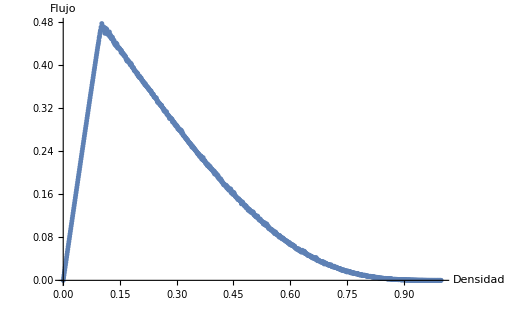

```mathematica
data = Import["C:\\Users\\Carlos\\Documents\\Maestria\\Sistemas Dinamicos\\Trafico\\FreewayAC\\Resultados\\Circular\\flow_total.csv"];
ListPlot[data, AxesLabel->{"Densidad", "Flujo"}]
```

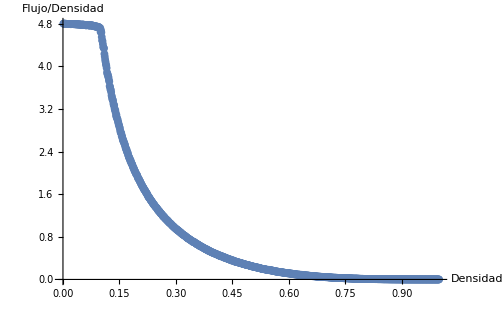

```mathematica
data = Import["C:\\Users\\Carlos\\Documents\\Maestria\\Sistemas Dinamicos\\Trafico\\FreewayAC\\Resultados\\Circular\\flow_per_density_total.csv"];
ListPlot[data, AxesLabel->{"Densidad", "Flujo/Densidad"}]
```

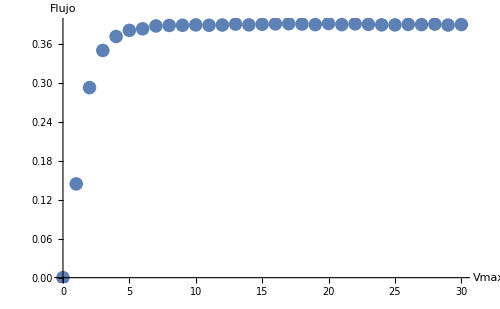

```mathematica
data = Import["C:\\Users\\Carlos\\Documents\\Maestria\\Sistemas Dinamicos\\Trafico\\FreewayAC\\Resultados\\Circular\\vmax_total.csv"];
ListPlot[data, AxesLabel->{"Vmax", "Flujo"}]
```

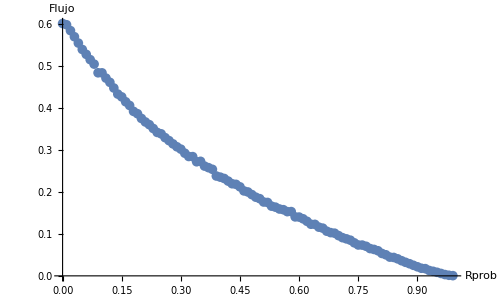

```mathematica
data = Import["C:\\Users\\Carlos\\Documents\\Maestria\\Sistemas Dinamicos\\Trafico\\FreewayAC\\Resultados\\Circular\\flow_vs_rand_prob.csv"];
ListPlot[data, AxesLabel->{"Rprob", "Flujo"}]
```

```mathematica
(* Auto inteligente *)
```

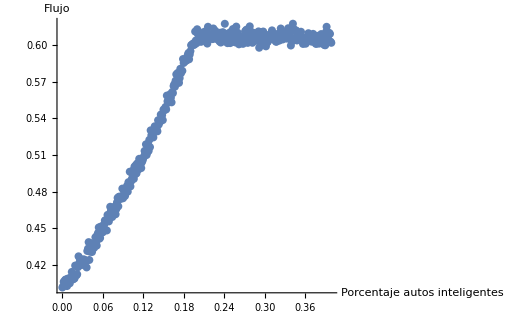

```mathematica
data = Import["C:\\Users\\Carlos\\Documents\\Maestria\\Sistemas Dinamicos\\Trafico\\FreewayAC\\Resultados\\Smart\\flow_vs_smart_car_density.csv"];
ListPlot[data, AxesLabel->{"Porcentaje \nautos inteligentes", "Flujo"}]
```

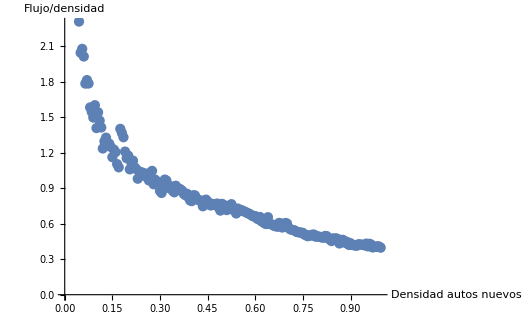

```mathematica
data = Import["C:\\Users\\Carlos\\Documents\\Maestria\\Sistemas Dinamicos\\Trafico\\FreewayAC\\Resultados\\Open\\flow_vs_smart_new_density.csv"];
ListPlot[data, AxesLabel->{"Densidad \nautos nuevos", "Flujo/densidad"}]
```